# Rigid bodies, plastic impact

-Graphics-

```mathematica
param={l1->2.0,l2->3.0,m1->10,m2->10,mb->100,m->15,r->1,θ->0.2};
```

## Kinematics

We start with a simple manipulator, moving base (that mimics the spacecraft position and orientation) and two rotational links.

```mathematica
Mrotztrasl[α_,point_]:={{Cos[α],-Sin[α],0,point[[1]]},{Sin[α],Cos[α],0,point[[2]]},{0,0,1,point[[3]]},{0,0,0,1}};
Mrotztrasl[α,{p1,p2,p3}]//MatrixForm
```

(Cos[α] | -Sin[α] | 0 | p1
Sin[α] | Cos[α] | 0 | p2
0 | 0 | 1 | p3
0 | 0 | 0 | 1)

```mathematica
M11=Mrotztrasl[θ1[t],{0,0,0}];
```

```mathematica
M01'=Mrotztrasl[0,{x[t],y[t],0}];
```

```mathematica
M01=M01'.M11;M01//MatrixForm
```

(Cos[θ1[t]] | -Sin[θ1[t]] | 0 | x[t]
Sin[θ1[t]] | Cos[θ1[t]] | 0 | y[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M01'=Mrotztrasl[θ1[t],{0,0,0}].Mrotztrasl[0,{x[t],y[t],0}];M01'//MatrixForm
```

(Cos[θ1[t]] | -Sin[θ1[t]] | 0 | Cos[θ1[t]] x[t]-Sin[θ1[t]] y[t]
Sin[θ1[t]] | Cos[θ1[t]] | 0 | Sin[θ1[t]] x[t]+Cos[θ1[t]] y[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M12=Mrotztrasl[θ2[t],{l1 Cos[θ2[t]],l1 Sin[θ2[t]],0}];M12//MatrixForm
```

(Cos[θ2[t]] | -Sin[θ2[t]] | 0 | l1 Cos[θ2[t]]
Sin[θ2[t]] | Cos[θ2[t]] | 0 | l1 Sin[θ2[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M23=Mrotztrasl[θ3[t],{l2 Cos[θ3[t]],l2 Sin[θ3[t]],0}];M23//MatrixForm
```

(Cos[θ3[t]] | -Sin[θ3[t]] | 0 | l2 Cos[θ3[t]]
Sin[θ3[t]] | Cos[θ3[t]] | 0 | l2 Sin[θ3[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M13=M12.M23;
```

```mathematica
M02=M01.M12;
```

```mathematica
M03=M02.M23;
```

### Origin points

```mathematica
origin={0,0,0,1};
```

```mathematica
O1=M01.origin;O1//MatrixForm
```

(x[t]
y[t]
0
1)

```mathematica
O2=M02.origin;O2//MatrixForm
```

(l1 Cos[θ1[t]] Cos[θ2[t]]-l1 Sin[θ1[t]] Sin[θ2[t]]+x[t]
l1 Cos[θ2[t]] Sin[θ1[t]]+l1 Cos[θ1[t]] Sin[θ2[t]]+y[t]
0
1)

```mathematica
O3=Simplify[M03.origin];O3//MatrixForm
```

(l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]]+x[t]
l1 Sin[θ1[t]+θ2[t]]+l2 Sin[θ1[t]+θ2[t]+θ3[t]]+y[t]
0
1)

Jacobian matrix:

```mathematica
J=FullSimplify[D[O3[[1;;2]],{{x[t],y[t],θ1[t],θ2[t],θ3[t]}}]];J//MatrixForm
```

(1 | 0 | -l1 Sin[θ1[t]+θ2[t]]-l2 Sin[θ1[t]+θ2[t]+θ3[t]] | -l1 Sin[θ1[t]+θ2[t]]-l2 Sin[θ1[t]+θ2[t]+θ3[t]] | -l2 Sin[θ1[t]+θ2[t]+θ3[t]]
0 | 1 | l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]] | l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]] | l2 Cos[θ1[t]+θ2[t]+θ3[t]])

```mathematica
J. D[{x[t],y[t],θ1[t],θ2[t],θ3[t]},t]==D[O3[[1;;2]],t]//Simplify
```

True

### Plot a 2D scheme of the robot

```mathematica
paramScheme={θ1[t]->0.2,θ2[t]->π/6,θ3[t]->π/6,x[t]->1,y[t]->2};
```

```mathematica
RobotPlot=ListLinePlot[{O1[[1;;2]]/.param/.paramScheme,O2[[1;;2]]/.param/.paramScheme,O3[[1;;2]]/.param/.paramScheme},PlotRange->{{0,7},{0,7}},PlotMarkers->{Automatic, 5}];
```

```mathematica
labels={"X0","Y0"};
```

```mathematica
For[i=1,i<3,i++,u={0,0};(*initializing u as a null 3 elements vector*)u⟦i⟧=1;(*Setting the i-th element of u equal to 1,to have a unit vector*)RF0arrow[i]=Graphics[{Thickness[0.010],Red,Arrowheads[0.04],
Text[labels⟦i⟧,2 u+0.07],Arrow[{{0,0},2 u}]},Axes->True]];
```

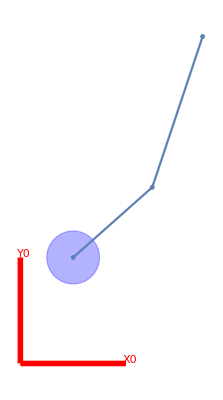

```mathematica
Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[O1[[1;;2]]/.param/.paramScheme,r]}]],RobotPlot,RF0arrow[1],RF0arrow[2]}]
```

```mathematica
O1[[1;;2]]/.param/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5}
```

{a1,a2}

```mathematica
paraml={l1->2.0,l2->3.0};
```

```mathematica
Manipulate[Show[{ListLinePlot[{O1[[1;;2]]/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5},O2[[1;;2]]/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5},O3[[1;;2]]/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5}}/.paraml,PlotRange->{{0,8},{0,8}},AspectRatio->1,PlotMarkers->{Automatic, 5}]},Block[{r=0.5},Graphics[{EdgeForm[Thick],Blue,Opacity[0.3],Disk[O1[[1;;2]]/.param/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5},r],Thickness[0.007],Opacity[0.5],Red,Arrowheads[0.04],Arrow[{O1[[1;;2]]/.param/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5},{(O1[[1;;2]]/.param/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5})[[1]]+l1 /.param/.paramScheme,(O1[[1;;2]]/.param/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5})[[2]]/.param/.paramScheme}}],Arrow[{O1[[1;;2]]/.param/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5},{(O1[[1;;2]]/.param/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5})[[1]]/.param/.paramScheme,(O1[[1;;2]]/.param/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5})[[2]]+l1/.param/.paramScheme}}],Blue,Arrow[{O1[[1;;2]]/.param/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5},{(O1[[1;;2]]/.param/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5})[[1]]-l1 Sin[a3]/.param/.paramScheme,(O1[[1;;2]]/.param/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5})[[2]]+l1 Cos[a3]/.param/.paramScheme}}],Arrow[{O1[[1;;2]]/.param/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5},{(O1[[1;;2]]/.param/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5})[[1]]+l1 Cos[a3]/.param/.paramScheme,(O1[[1;;2]]/.param/.{x[t]->a1,y[t]->a2,θ1[t]->a3,θ2[t]->a4,θ3[t]->a5})[[2]]+l1 Sin[a3]/.param/.paramScheme}}]}]],RF0arrow[1],RF0arrow[2]],{a1,0,3},{a2,0,3},{a3,0,π/4},{a4,0,π/4},{a5,0,π/4}]
```

## Dynamics

## Manipulator

### IR method

The mass is considered distributed, hence the pseudo inertia tensor can be written like this:

```mathematica
Ixx1=1/4 mb r^2;
Iyy1=1/4 mb r^2;
Izz1=0;
Ixx2=1/3m1 l1^2;
Ixx3=1/3 m2 l2^2;
```

Inertia frame in the com of the round base:

```mathematica
J11={{Ixx1,0,0,0},{0,Iyy1,0,0},{0,0,Izz1,0},{0,0,0,mb}};J11//MatrixForm
```

((mb r^2)/4 | 0 | 0 | 0
0 | (mb r^2)/4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | mb)

```mathematica
J10=Simplify[M01.J11.Transpose[M01]];J10//MatrixForm
```

(1/4 mb (r^2+4 x[t]^2) | mb x[t] y[t] | 0 | mb x[t]
mb x[t] y[t] | 1/4 mb (r^2+4 y[t]^2) | 0 | mb y[t]
0 | 0 | 0 | 0
mb x[t] | mb y[t] | 0 | mb)

```mathematica
J22={{Ixx2,0,0,-l1/2 m1},{0,0,0,0},{0,0,0,0},{-l1/2 m1,0,0,m1}};J22//MatrixForm
```

((l1^2 m1)/3 | 0 | 0 | -(l1 m1)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l1 m1)/2 | 0 | 0 | m1)

```mathematica
J20=Simplify[M02.J22.Transpose[M02]];
```

```mathematica
J33={{Ixx3,0,0,-l2/2 m2},{0,0,0,0},{0,0,0,0},{-l2/2 m2,0,0,m2}};J33//MatrixForm
```

((l2^2 m2)/3 | 0 | 0 | -(l2 m2)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l2 m2)/2 | 0 | 0 | m2)

```mathematica
J30=Simplify[M03.J33.Transpose[M03]];
```

```mathematica
W01=Simplify[D[M01,t].Inverse[M01]];W01//MatrixForm
```

(0 | -θ1'[t] | 0 | x'[t]+y[t] θ1'[t]
θ1'[t] | 0 | 0 | y'[t]-x[t] θ1'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W01'=Simplify[D[M01',t].Inverse[M01']];W01'//MatrixForm
```

(0 | -θ1'[t] | 0 | Cos[θ1[t]] x'[t]-Sin[θ1[t]] y'[t]
θ1'[t] | 0 | 0 | Sin[θ1[t]] x'[t]+Cos[θ1[t]] y'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W11=Simplify[D[M11,t].Inverse[M11]];W11//MatrixForm
```

(0 | -θ1'[t] | 0 | 0
θ1'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L01x=({{0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
L01y=({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

```mathematica
L11=W11/θ1'[t];
```

```mathematica
L11F0=Simplify[M01.L11.Inverse[M01]];L11F0//MatrixForm
```

(0 | -1 | 0 | y[t]
1 | 0 | 0 | -x[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W12=Simplify[D[M12,t].Inverse[M12]];W12//MatrixForm
```

(0 | -θ2'[t] | 0 | 0
θ2'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L12=W12/θ2'[t];
```

```mathematica
L12F0=Simplify[M01.L12.Inverse[M01]];L12F0//MatrixForm
```

(0 | -1 | 0 | y[t]
1 | 0 | 0 | -x[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W02=Simplify[D[M02,t].Inverse[M02]];W02//MatrixForm
```

(0 | -θ1'[t]-θ2'[t] | 0 | x'[t]+y[t] (θ1'[t]+θ2'[t])
θ1'[t]+θ2'[t] | 0 | 0 | y'[t]-x[t] (θ1'[t]+θ2'[t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
H02=D[M02,t,t].Inverse[M02];
```

```mathematica
W23=Simplify[D[M23,t].Inverse[M23]];W23//MatrixForm
```

(0 | -θ3'[t] | 0 | 0
θ3'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L23=W23/θ3'[t];
L23F0=Simplify[M02.L23.Inverse[M02]];L23F0//MatrixForm
```

(0 | -1 | 0 | l1 Sin[θ1[t]+θ2[t]]+y[t]
1 | 0 | 0 | -l1 Cos[θ1[t]+θ2[t]]-x[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W03=Simplify[D[M03,t].Inverse[M03]];W03//MatrixForm
```

(0 | -θ1'[t]-θ2'[t]-θ3'[t] | 0 | x'[t]+l1 Sin[θ1[t]+θ2[t]] θ3'[t]+y[t] (θ1'[t]+θ2'[t]+θ3'[t])
θ1'[t]+θ2'[t]+θ3'[t] | 0 | 0 | y'[t]-l1 Cos[θ1[t]+θ2[t]] θ3'[t]-x[t] (θ1'[t]+θ2'[t]+θ3'[t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
H03=D[M03,t,t].Inverse[M03];
```

```mathematica
T1=Simplify[1/2Tr[W01.J10.Transpose[W01]]];
T2=Simplify[1/2Tr[W02.J20.Transpose[W02]]];
T3=Simplify[1/2Tr[W03.J30.Transpose[W03]]];
```

The potential energy of body i, denoted by Ui, consists of two parts; one due to the gravity gradient and the other due to the elastic strain energy stored in the flexible body. The effect of the former is much smaller than the latter and is neglected here. Hence the potential energy of a rigid body is equal to zero.

```mathematica
L=T1+T2+T3;
```

By neglecting the constraints forces (since they don’t affect the lagrange equation), we get the actions matrices:

```mathematica
actionMatrix[cx_,cy_,cz_,fx_,fy_,fz_]:={{0,-cz,cy,fx},{cz,0,-cx,fy},{-cy,cx,0,fz},{-fx,-fy,-fz,0}};
```

```mathematica
ϕ11=actionMatrix[0,0,τ1-τ2,Fx,Fy,0];ϕ11//MatrixForm
```

(0 | -τ1+τ2 | 0 | Fx
τ1-τ2 | 0 | 0 | Fy
0 | 0 | 0 | 0
-Fx | -Fy | 0 | 0)

```mathematica
ϕ10=M01.ϕ11.Transpose[M01];
```

```mathematica
ϕ22=actionMatrix[0,0,τ2-τ3-τ1,-Fx,-Fy,0];ϕ22//MatrixForm
ϕ20=FullSimplify[M02.ϕ22.Transpose[M02]];ϕ20//MatrixForm
```

(0 | τ1-τ2+τ3 | 0 | -Fx
-τ1+τ2-τ3 | 0 | 0 | -Fy
0 | 0 | 0 | 0
Fx | Fy | 0 | 0)

(0 | Fy l1+τ1-τ2+τ3+(Fy Cos[θ1[t]+θ2[t]]+Fx Sin[θ1[t]+θ2[t]]) x[t]+(-Fx Cos[θ1[t]+θ2[t]]+Fy Sin[θ1[t]+θ2[t]]) y[t] | 0 | -Fx Cos[θ1[t]+θ2[t]]+Fy Sin[θ1[t]+θ2[t]]
-Fy l1-τ1+τ2-τ3-(Fy Cos[θ1[t]+θ2[t]]+Fx Sin[θ1[t]+θ2[t]]) x[t]+(Fx Cos[θ1[t]+θ2[t]]-Fy Sin[θ1[t]+θ2[t]]) y[t] | 0 | 0 | -Fy Cos[θ1[t]+θ2[t]]-Fx Sin[θ1[t]+θ2[t]]
0 | 0 | 0 | 0
Fx Cos[θ1[t]+θ2[t]]-Fy Sin[θ1[t]+θ2[t]] | Fy Cos[θ1[t]+θ2[t]]+Fx Sin[θ1[t]+θ2[t]] | 0 | 0)

```mathematica
FullSimplify[H02.J20-Transpose[H02.J20]]//MatrixForm
```

(0 | 1/6 m1 (-l1 (-3 Sin[θ1[t]+θ2[t]] x''[t]+3 Cos[θ1[t]+θ2[t]] y''[t]+2 l1 (θ1''[t]+θ2''[t]))+3 x[t] (l1 Sin[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t])^2-2 y''[t]-l1 Cos[θ1[t]+θ2[t]] (θ1''[t]+θ2''[t]))-3 y[t] (l1 Cos[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t])^2-2 x''[t]+l1 Sin[θ1[t]+θ2[t]] (θ1''[t]+θ2''[t]))) | 0 | -1/2 m1 (l1 Cos[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t])^2-2 x''[t]+l1 Sin[θ1[t]+θ2[t]] (θ1''[t]+θ2''[t]))
1/6 m1 (l1 (-3 Sin[θ1[t]+θ2[t]] x''[t]+3 Cos[θ1[t]+θ2[t]] y''[t]+2 l1 (θ1''[t]+θ2''[t]))+3 x[t] (-l1 Sin[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t])^2+2 y''[t]+l1 Cos[θ1[t]+θ2[t]] (θ1''[t]+θ2''[t]))+3 y[t] (l1 Cos[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t])^2-2 x''[t]+l1 Sin[θ1[t]+θ2[t]] (θ1''[t]+θ2''[t]))) | 0 | 0 | 1/2 m1 (-l1 Sin[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t])^2+2 y''[t]+l1 Cos[θ1[t]+θ2[t]] (θ1''[t]+θ2''[t]))
0 | 0 | 0 | 0
1/2 m1 (l1 Cos[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t])^2-2 x''[t]+l1 Sin[θ1[t]+θ2[t]] (θ1''[t]+θ2''[t])) | 1/2 m1 (l1 Sin[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t])^2-2 y''[t]-l1 Cos[θ1[t]+θ2[t]] (θ1''[t]+θ2''[t])) | 0 | 0)

```mathematica
ϕ33=actionMatrix[0,0,τ3,0,0,0];
ϕ30=M03.ϕ33.Transpose[M03];ϕ30//MatrixForm
```

(0 | -τ3 (Cos[θ3[t]] (Cos[θ1[t]] Cos[θ2[t]]-Sin[θ1[t]] Sin[θ2[t]])+(-Cos[θ2[t]] Sin[θ1[t]]-Cos[θ1[t]] Sin[θ2[t]]) Sin[θ3[t]]) (Cos[θ3[t]] (Cos[θ1[t]] Cos[θ2[t]]-Sin[θ1[t]] Sin[θ2[t]])-(Cos[θ2[t]] Sin[θ1[t]]+Cos[θ1[t]] Sin[θ2[t]]) Sin[θ3[t]])+τ3 (Cos[θ3[t]] (-Cos[θ2[t]] Sin[θ1[t]]-Cos[θ1[t]] Sin[θ2[t]])-(Cos[θ1[t]] Cos[θ2[t]]-Sin[θ1[t]] Sin[θ2[t]]) Sin[θ3[t]]) (Cos[θ3[t]] (Cos[θ2[t]] Sin[θ1[t]]+Cos[θ1[t]] Sin[θ2[t]])+(Cos[θ1[t]] Cos[θ2[t]]-Sin[θ1[t]] Sin[θ2[t]]) Sin[θ3[t]]) | 0 | 0
τ3 (Cos[θ3[t]] (Cos[θ1[t]] Cos[θ2[t]]-Sin[θ1[t]] Sin[θ2[t]])+(-Cos[θ2[t]] Sin[θ1[t]]-Cos[θ1[t]] Sin[θ2[t]]) Sin[θ3[t]]) (Cos[θ3[t]] (Cos[θ1[t]] Cos[θ2[t]]-Sin[θ1[t]] Sin[θ2[t]])-(Cos[θ2[t]] Sin[θ1[t]]+Cos[θ1[t]] Sin[θ2[t]]) Sin[θ3[t]])-τ3 (Cos[θ3[t]] (-Cos[θ2[t]] Sin[θ1[t]]-Cos[θ1[t]] Sin[θ2[t]])-(Cos[θ1[t]] Cos[θ2[t]]-Sin[θ1[t]] Sin[θ2[t]]) Sin[θ3[t]]) (Cos[θ3[t]] (Cos[θ2[t]] Sin[θ1[t]]+Cos[θ1[t]] Sin[θ2[t]])+(Cos[θ1[t]] Cos[θ2[t]]-Sin[θ1[t]] Sin[θ2[t]]) Sin[θ3[t]]) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Simplify[H03.J30-Transpose[H03.J30]]//MatrixForm
```

(0 | -1/6 m2 (-6 l1 l2 Sin[θ3[t]] θ1'[t] θ3'[t]-6 l1 l2 Sin[θ3[t]] θ2'[t] θ3'[t]-3 l1 l2 Sin[θ3[t]] θ3'[t]^2-6 l1 Sin[θ1[t]+θ2[t]] x''[t]-3 l2 Sin[θ1[t]+θ2[t]+θ3[t]] x''[t]+6 l1 Cos[θ1[t]+θ2[t]] y''[t]+3 l2 Cos[θ1[t]+θ2[t]+θ3[t]] y''[t]+6 l1^2 θ1''[t]+2 l2^2 θ1''[t]+6 l1 l2 Cos[θ3[t]] θ1''[t]+6 l1^2 θ2''[t]+2 l2^2 θ2''[t]+6 l1 l2 Cos[θ3[t]] θ2''[t]+2 l2^2 θ3''[t]+3 l1 l2 Cos[θ3[t]] θ3''[t]-3 x[t] ((2 l1 Sin[θ1[t]+θ2[t]]+l2 Sin[θ1[t]+θ2[t]+θ3[t]]) θ1'[t]^2+(2 l1 Sin[θ1[t]+θ2[t]]+l2 Sin[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]^2+2 l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ2'[t] θ3'[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ3'[t]^2+2 θ1'[t] ((2 l1 Sin[θ1[t]+θ2[t]]+l2 Sin[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ3'[t])-2 y''[t]-2 l1 Cos[θ1[t]+θ2[t]] θ1''[t]-l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ1''[t]-2 l1 Cos[θ1[t]+θ2[t]] θ2''[t]-l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ2''[t]-l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ3''[t])+3 y[t] ((2 l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]]) θ1'[t]^2+(2 l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]^2+2 l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ2'[t] θ3'[t]+l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ3'[t]^2+2 θ1'[t] ((2 l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]+l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ3'[t])-2 x''[t]+2 l1 Sin[θ1[t]+θ2[t]] θ1''[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ1''[t]+2 l1 Sin[θ1[t]+θ2[t]] θ2''[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ2''[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ3''[t])) | 0 | -1/2 m2 ((2 l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]]) θ1'[t]^2+(2 l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]^2+2 l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ2'[t] θ3'[t]+l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ3'[t]^2+2 θ1'[t] ((2 l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]+l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ3'[t])-2 x''[t]+2 l1 Sin[θ1[t]+θ2[t]] θ1''[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ1''[t]+2 l1 Sin[θ1[t]+θ2[t]] θ2''[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ2''[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ3''[t])
1/6 m2 (-6 l1 l2 Sin[θ3[t]] θ1'[t] θ3'[t]-6 l1 l2 Sin[θ3[t]] θ2'[t] θ3'[t]-3 l1 l2 Sin[θ3[t]] θ3'[t]^2-6 l1 Sin[θ1[t]+θ2[t]] x''[t]-3 l2 Sin[θ1[t]+θ2[t]+θ3[t]] x''[t]+6 l1 Cos[θ1[t]+θ2[t]] y''[t]+3 l2 Cos[θ1[t]+θ2[t]+θ3[t]] y''[t]+6 l1^2 θ1''[t]+2 l2^2 θ1''[t]+6 l1 l2 Cos[θ3[t]] θ1''[t]+6 l1^2 θ2''[t]+2 l2^2 θ2''[t]+6 l1 l2 Cos[θ3[t]] θ2''[t]+2 l2^2 θ3''[t]+3 l1 l2 Cos[θ3[t]] θ3''[t]-3 x[t] ((2 l1 Sin[θ1[t]+θ2[t]]+l2 Sin[θ1[t]+θ2[t]+θ3[t]]) θ1'[t]^2+(2 l1 Sin[θ1[t]+θ2[t]]+l2 Sin[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]^2+2 l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ2'[t] θ3'[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ3'[t]^2+2 θ1'[t] ((2 l1 Sin[θ1[t]+θ2[t]]+l2 Sin[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ3'[t])-2 y''[t]-2 l1 Cos[θ1[t]+θ2[t]] θ1''[t]-l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ1''[t]-2 l1 Cos[θ1[t]+θ2[t]] θ2''[t]-l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ2''[t]-l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ3''[t])+3 y[t] ((2 l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]]) θ1'[t]^2+(2 l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]^2+2 l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ2'[t] θ3'[t]+l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ3'[t]^2+2 θ1'[t] ((2 l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]+l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ3'[t])-2 x''[t]+2 l1 Sin[θ1[t]+θ2[t]] θ1''[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ1''[t]+2 l1 Sin[θ1[t]+θ2[t]] θ2''[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ2''[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ3''[t])) | 0 | 0 | -1/2 m2 ((2 l1 Sin[θ1[t]+θ2[t]]+l2 Sin[θ1[t]+θ2[t]+θ3[t]]) θ1'[t]^2+(2 l1 Sin[θ1[t]+θ2[t]]+l2 Sin[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]^2+2 l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ2'[t] θ3'[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ3'[t]^2+2 θ1'[t] ((2 l1 Sin[θ1[t]+θ2[t]]+l2 Sin[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ3'[t])-2 y''[t]-2 l1 Cos[θ1[t]+θ2[t]] θ1''[t]-l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ1''[t]-2 l1 Cos[θ1[t]+θ2[t]] θ2''[t]-l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ2''[t]-l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ3''[t])
0 | 0 | 0 | 0
1/2 m2 ((2 l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]]) θ1'[t]^2+(2 l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]^2+2 l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ2'[t] θ3'[t]+l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ3'[t]^2+2 θ1'[t] ((2 l1 Cos[θ1[t]+θ2[t]]+l2 Cos[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]+l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ3'[t])-2 x''[t]+2 l1 Sin[θ1[t]+θ2[t]] θ1''[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ1''[t]+2 l1 Sin[θ1[t]+θ2[t]] θ2''[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ2''[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ3''[t]) | 1/2 m2 ((2 l1 Sin[θ1[t]+θ2[t]]+l2 Sin[θ1[t]+θ2[t]+θ3[t]]) θ1'[t]^2+(2 l1 Sin[θ1[t]+θ2[t]]+l2 Sin[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]^2+2 l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ2'[t] θ3'[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ3'[t]^2+2 θ1'[t] ((2 l1 Sin[θ1[t]+θ2[t]]+l2 Sin[θ1[t]+θ2[t]+θ3[t]]) θ2'[t]+l2 Sin[θ1[t]+θ2[t]+θ3[t]] θ3'[t])-2 y''[t]-2 l1 Cos[θ1[t]+θ2[t]] θ1''[t]-l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ1''[t]-2 l1 Cos[θ1[t]+θ2[t]] θ2''[t]-l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ2''[t]-l2 Cos[θ1[t]+θ2[t]+θ3[t]] θ3''[t]) | 0 | 0)

Let’s derivate the non-lagrangian components:

```mathematica
PSS[Mat1_,Mat2_]:=Mat1[[3,2]]*Mat2[[3,2]]+Mat1[[1,3]]*Mat2[[1,3]]+Mat1[[2,1]]*Mat2[[2,1]]+Mat1[[1,4]]*Mat2[[1,4]]+Mat1[[2,4]]*Mat2[[2,4]]+Mat1[[3,4]]*Mat2[[3,4]];
```

```mathematica
f1=FullSimplify[PSS[(ϕ10+ϕ20+ϕ30),L01x]]
f2=FullSimplify[PSS[(ϕ10+ϕ20+ϕ30),L01y]]
f3=FullSimplify[PSS[(ϕ10+ϕ20+ϕ30),L11F0]]
f4=FullSimplify[PSS[(ϕ20+ϕ30),L12F0]]
f5=Simplify[PSS[(ϕ30),L23F0]]
```

Fx Cos[θ1[t]]-Fy Sin[θ1[t]]

Fy Cos[θ1[t]]+Fx Sin[θ1[t]]

τ1

τ2

τ3

```mathematica
eq1=Simplify[D[D[L,x'[t]],t]-D[L,x[t]]-f1];
eq2=Simplify[D[D[L,y'[t]],t]-D[L,y[t]]-f2];
eq3=Simplify[D[D[L,θ1'[t]],t]-D[L,θ1[t]]-f3];
eq4=Simplify[D[D[L,θ2'[t]],t]-D[L,θ2[t]]-f4];
eq5=Simplify[D[D[L,θ3'[t]],t]-D[L,θ3[t]]-f5];
```

```mathematica
{c,M}=FullSimplify[Normal@CoefficientArrays[{eq1,eq2,eq3,eq4,eq5},{x''[t],y''[t],θ1''[t],θ2''[t],θ3''[t]}]];
```

```mathematica
MatrixForm[M]
```

(m1+m2+mb | 0 | 1/2 (-l1 (m1+2 m2) Sin[θ1[t]+θ2[t]]-l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]) | 1/2 (-l1 (m1+2 m2) Sin[θ1[t]+θ2[t]]-l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]) | -1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]
0 | m1+m2+mb | 1/2 (l1 (m1+2 m2) Cos[θ1[t]+θ2[t]]+l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]) | 1/2 (l1 (m1+2 m2) Cos[θ1[t]+θ2[t]]+l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]) | 1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]
1/2 (-l1 (m1+2 m2) Sin[θ1[t]+θ2[t]]-l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]) | 1/2 (l1 (m1+2 m2) Cos[θ1[t]+θ2[t]]+l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]) | 1/6 (2 l2^2 m2+2 l1^2 (m1+3 m2)+3 mb r^2+6 l1 l2 m2 Cos[θ3[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[θ3[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[θ3[t]])
1/2 (-l1 (m1+2 m2) Sin[θ1[t]+θ2[t]]-l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]) | 1/2 (l1 (m1+2 m2) Cos[θ1[t]+θ2[t]]+l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[θ3[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[θ3[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[θ3[t]])
-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] | 1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] | 1/6 l2 m2 (2 l2+3 l1 Cos[θ3[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[θ3[t]]) | (l2^2 m2)/3)

```mathematica
MatrixForm[c]
```

(1/2 (-2 Fx Cos[θ1[t]]+2 Fy Sin[θ1[t]]-l1 (m1+2 m2) Cos[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t])^2-l2 m2 Cos[θ1[t]+θ2[t]] Cos[θ3[t]] (θ1'[t]+θ2'[t]+θ3'[t])^2+l2 m2 Sin[θ1[t]+θ2[t]] Sin[θ3[t]] (θ1'[t]+θ2'[t]+θ3'[t])^2)
1/2 (-2 (Fy Cos[θ1[t]]+Fx Sin[θ1[t]])-l1 (m1+2 m2) Sin[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t])^2-l2 m2 Cos[θ3[t]] Sin[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t]+θ3'[t])^2-l2 m2 Cos[θ1[t]+θ2[t]] Sin[θ3[t]] (θ1'[t]+θ2'[t]+θ3'[t])^2)
-τ1-1/2 l1 l2 m2 Sin[θ3[t]] θ3'[t] (2 (θ1'[t]+θ2'[t])+θ3'[t])
-τ2-1/2 l1 l2 m2 Sin[θ3[t]] θ3'[t] (2 (θ1'[t]+θ2'[t])+θ3'[t])
-τ3+1/2 l1 l2 m2 Sin[θ3[t]] (θ1'[t]+θ2'[t])^2)

Equation of motion: Mp^(..)+ c = u

### Classic Lagrangian method

```mathematica
O12D=(M01.{0,0,0,1})[[1;;2]];
O22D=(M02.{-l1/2,0,0,1})[[1;;2]];
O32D=(M03.{-l2/2,0,0,1})[[1;;2]];
```

```mathematica
v1=D[O12D,t];
v2=D[O22D,t];
v3=D[O32D,t];
```

```mathematica
v1square=Simplify[v1[[1]]^2+v1[[2]]^2];
v2square=Simplify[v2[[1]]^2+v2[[2]]^2];
v3square=Simplify[v3[[1]]^2+v3[[2]]^2];
```

Inertia wrt CoM:

```mathematica
I1=1/2mb r^2;
I2=1/12m1 l1^2;
I3=1/12m2 l2^2;
```

```mathematica
k1mid=1/2mb v1square+1/2I1 θ1'[t]^2;
k2mid=1/2m1 v2square+1/2I2 (θ1'[t]+θ2'[t])^2;
k3mid=1/2m2 v3square+1/2I3 (θ1'[t]+θ2'[t]+θ3'[t])^2;
```

```mathematica
lmid=k1mid+k2mid+k3mid;
```

```mathematica
eq1Mid=Simplify[D[D[lmid,x'[t]],t]-D[lmid,x[t]]-f1];
eq2Mid=Simplify[D[D[lmid,y'[t]],t]-D[lmid,y[t]]-f2];
eq3Mid=Simplify[D[D[lmid,θ1'[t]],t]-D[lmid,θ1[t]]-f3];
eq4Mid=Simplify[D[D[lmid,θ2'[t]],t]-D[lmid,θ2[t]]-f4];
eq5Mid=Simplify[D[D[lmid,θ3'[t]],t]-D[lmid,θ3[t]]-f5];
```

```mathematica
{c2,M2}=FullSimplify[Normal@CoefficientArrays[{eq1Mid,eq2Mid,eq3Mid,eq4Mid,eq5Mid},{x''[t],y''[t],θ1''[t],θ2''[t],θ3''[t]}]];
```

```mathematica
MatrixForm[M2]
```

(m1+m2+mb | 0 | 1/2 (-l1 (m1+2 m2) Sin[θ1[t]+θ2[t]]-l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]) | 1/2 (-l1 (m1+2 m2) Sin[θ1[t]+θ2[t]]-l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]) | -1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]
0 | m1+m2+mb | 1/2 (l1 (m1+2 m2) Cos[θ1[t]+θ2[t]]+l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]) | 1/2 (l1 (m1+2 m2) Cos[θ1[t]+θ2[t]]+l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]) | 1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]
1/2 (-l1 (m1+2 m2) Sin[θ1[t]+θ2[t]]-l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]) | 1/2 (l1 (m1+2 m2) Cos[θ1[t]+θ2[t]]+l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]) | 1/6 (2 l2^2 m2+2 l1^2 (m1+3 m2)+3 mb r^2+6 l1 l2 m2 Cos[θ3[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[θ3[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[θ3[t]])
1/2 (-l1 (m1+2 m2) Sin[θ1[t]+θ2[t]]-l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]]) | 1/2 (l1 (m1+2 m2) Cos[θ1[t]+θ2[t]]+l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[θ3[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[θ3[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[θ3[t]])
-1/2 l2 m2 Sin[θ1[t]+θ2[t]+θ3[t]] | 1/2 l2 m2 Cos[θ1[t]+θ2[t]+θ3[t]] | 1/6 l2 m2 (2 l2+3 l1 Cos[θ3[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[θ3[t]]) | (l2^2 m2)/3)

```mathematica
MatrixForm[c2]
```

(1/2 (-2 Fx Cos[θ1[t]]+2 Fy Sin[θ1[t]]-l1 (m1+2 m2) Cos[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t])^2-l2 m2 Cos[θ1[t]+θ2[t]] Cos[θ3[t]] (θ1'[t]+θ2'[t]+θ3'[t])^2+l2 m2 Sin[θ1[t]+θ2[t]] Sin[θ3[t]] (θ1'[t]+θ2'[t]+θ3'[t])^2)
1/2 (-2 (Fy Cos[θ1[t]]+Fx Sin[θ1[t]])-l1 (m1+2 m2) Sin[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t])^2-l2 m2 Cos[θ3[t]] Sin[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t]+θ3'[t])^2-l2 m2 Cos[θ1[t]+θ2[t]] Sin[θ3[t]] (θ1'[t]+θ2'[t]+θ3'[t])^2)
-τ1-1/2 l1 l2 m2 Sin[θ3[t]] θ3'[t] (2 (θ1'[t]+θ2'[t])+θ3'[t])
-τ2-1/2 l1 l2 m2 Sin[θ3[t]] θ3'[t] (2 (θ1'[t]+θ2'[t])+θ3'[t])
-τ3+1/2 l1 l2 m2 Sin[θ3[t]] (θ1'[t]+θ2'[t])^2)

```mathematica
FullSimplify[c2==c]
```

True

```mathematica
FullSimplify[M[[1]]==M2[[1]]]
FullSimplify[M[[2]]==M2[[2]]]
FullSimplify[M[[3]]==M2[[3]]]
FullSimplify[M[[4]]==M2[[4]]]
FullSimplify[M[[5]]==M2[[5]]]
```

True

True

True

«2 more identical outputs»

### Newton-Euler method

## Object

Let’s consider a circula spinning satellite. In 2D, we have 3 DoF: x, y, and rotation around z.
Coordinats refered to the COM:

```mathematica
ψ={X[t],Y[t],Ω[t]};
ψ'=D[ψ,t];
```

The jacobian describe the relationship between the velocity of the dof and the contact point:

```mathematica
Ms01=Mrotztrasl[Ω[t],{r Cos[θ],r Sin[θ],0}];Ms01//MatrixForm
```

(Cos[Ω[t]] | -Sin[Ω[t]] | 0 | r Cos[θ]
Sin[Ω[t]] | Cos[Ω[t]] | 0 | r Sin[θ]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
contactPlocal=Ms01.origin;
contactP=Simplify[{X[t],Y[t]}+Ms01[[1;;2,1;;2]].contactPlocal[[1;;2]]];contactP//MatrixForm
velContactP=D[contactP,t];velContactP//MatrixForm
```

(r Cos[θ+Ω[t]]+X[t]
r Sin[θ+Ω[t]]+Y[t])

(X'[t]-r Sin[θ+Ω[t]] Ω'[t]
Y'[t]+r Cos[θ+Ω[t]] Ω'[t])

```mathematica
Jo=D[contactP,{{X[t],Y[t],Ω[t]}}];Jo//MatrixForm
```

(1 | 0 | -r Sin[θ+Ω[t]]
0 | 1 | r Cos[θ+Ω[t]])

```mathematica
Transpose[Jo]//MatrixForm
```

(1 | 0
0 | 1
-r Sin[θ+Ω[t]] | r Cos[θ+Ω[t]])

```mathematica
Jo.ψ'==velContactP//Simplify
```

True

```mathematica
Iz=1/2m r^2;
```

```mathematica
T=1/2 m(ψ'[[1]]^2+ψ'[[2]]^2)+1/2Iz ψ'[[3]]^2;
```

```mathematica
eq1o=Simplify[D[D[T,X'[t]],t]-D[T,X[t]]-fx==0];
eq2o=Simplify[D[D[T,Y'[t]],t]-D[T,Y[t]]-fy==0];
eq3o=Simplify[D[D[T,Ω'[t]],t]-D[T,Ω[t]]-Τ==0];
(*eq4S=Simplify[D[D[T,θ'[t]],t]-D[T,θ[t]]-ϕ==0];*)
```

```mathematica
solo=Solve[{eq1o,eq2o,eq3o},{fx,fy,Τ}][[1]];
Eq1o=solo[[1,2]];
Eq2o=solo[[2,2]];
Eq3o=solo[[3,2]];
(*Eq4S=solS[[4,2]];*)
```

```mathematica
{co,Mo}=Normal@CoefficientArrays[{Eq1o,Eq2o,Eq3o},{X''[t],Y''[t],Ω''[t]}];
```

```mathematica
Mo//MatrixForm
```

(m | 0 | 0
0 | m | 0
0 | 0 | (m r^2)/2)

```mathematica
co//MatrixForm
```

(0
0
0)

## Impact

## Pre-impact

Following the 2007 paper, we can find the final condition of the manipulator after the impact:

```mathematica
Jo//MatrixForm
```

(1 | 0 | -r Sin[θ+Ω[t]]
0 | 1 | r Cos[θ+Ω[t]])

In the 2007 paper, there is an error when calculating the pseudo-inverse. The correct is the following:

```mathematica
pseudoInverseJo=Transpose[Jo].Inverse[Jo.Transpose[Jo]]//Simplify;pseudoInverseJo//MatrixForm
```

((2+r^2+r^2 Cos[2 (θ+Ω[t])])/(2 (1+r^2)) | (r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2)
(r^2 Cos[θ+Ω[t]] Sin[θ+Ω[t]])/(1+r^2) | (2+r^2-r^2 Cos[2 (θ+Ω[t])])/(2 (1+r^2))
-(r Sin[θ+Ω[t]])/(1+r^2) | (r Cos[θ+Ω[t]])/(1+r^2))

```mathematica
G=M2+Transpose[J].Transpose[pseudoInverseJo].Mo.pseudoInverseJo.J//FullSimplify ;
```

```mathematica
p={x[t],y[t],θ1[t],θ2[t],θ3[t]};
p'=D[p,t];
```

```mathematica
ψ={X[t],Y[t],Ω[t]};
ψ'=D[ψ,t];
```

```mathematica
H=M2. p'+Transpose[J].Transpose[pseudoInverseJo].Mo.ψ'//Simplify;
```

```mathematica
Det[G]
```

```mathematica
G/.param/.paramScheme/.{θ->0.1,Ω[t]->0.2}//MatrixForm
```

(133.578 | 3.36261 | -82.4369 | -82.4369 | -49.6344
3.36261 | 127.047 | 30.5197 | 30.5197 | 1.9276
-82.4369 | 30.5197 | 427.366 | 377.366 | 219.127
-82.4369 | 30.5197 | 377.366 | 377.366 | 219.127
-49.6344 | 1.9276 | 219.127 | 219.127 | 150.514)

```mathematica
Det[G/.param/.paramScheme/.{θ->0.1,Ω[t]->0.2}]
```

5.73696×10^9

Final values of the general coordinated of the base+manipulator after the impact:

```mathematica
pf'=Inverse[G].H ;
```

Final values of the satellite after the impact:

```mathematica
ψf'=pseudoInverseJo.J.pf';
```

### Initial conditions

Let’s suppose initial zero velocities of the BM system.

```mathematica
EEi=O3[[1;;2]]/.param/.paramScheme;
```

```mathematica
contactP/.param/.Ω[t]->0.1
```

{0.955336+X[t],0.29552+Y[t]}

```mathematica
jointPoint=(Solve[{EEi[[1]]==(contactP/.param/.Ω[t]->0.1)[[1]],EEi[[2]]==(contactP/.param/.Ω[t]->0.1)[[2]]},{X[t],Y[t]}])[[1]]
```

{X[t]→2.49746,Y[t]→5.87294}

```mathematica
initialConditions1={x[t]->0,y[t]->0,θ1[t]->0.2,θ2[t]->π/6,θ3[t]->π/6,X[t]->jointPoint[[1,2]],Y[t]->jointPoint[[2,2]],Ω[t]->0.1,
x'[t]->0,y'[t]->0,θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,X'[t]->-1,Y'[t]->0,Ω'[t]->0};
initialConditions2={x[t]->0,y[t]->0,θ1[t]->0.2,θ2[t]->π/6,θ3[t]->π/6,X[t]->jointPoint[[1,2]],Y[t]->jointPoint[[2,2]],Ω[t]->0.1,
x'[t]->0,y'[t]->0,θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,X'[t]->0,Y'[t]->-1,Ω'[t]->0};
```

```mathematica
pf1'=pf'/.initialConditions1/.param
pf2'=pf'/.initialConditions2/.param
```

{-0.0165433,-0.0153534,-1.32947×10^-15,-0.0348494,0.290324}

{-0.0343558,-0.03331,9.34998×10^-17,-0.139667,0.183142}

```mathematica
ψf1'=ψf'/.initialConditions1/.param
ψf2'=ψf'/.initialConditions2/.param
```

{-0.641744,-0.0026441,0.187122}

{-0.0026441,-0.105572,-0.100075}

```mathematica
((Jo.ψf')/.initialConditions1/.param)==((J.pf')/.initialConditions1/.param)
```

True

## Post-impact dynamics

```mathematica
EE=O3[[1;;2]]/.param;
```

After the capture, we assume that the object is now perfectly attached to the EE, hence its variables coincides with the ones of the EE. We also assume that the spinning velocity is resetted:

```mathematica
ψp={EE[[1]],EE[[2]],Ω[t]/.initialConditions1};
ψp'=D[{EE[[1]],EE[[2]],0},t];
```

We can now write the Jacobian matrix of the object as a function of the EE:

```mathematica
EEsubst={ψ[[1]]->ψp[[1]],ψ[[2]]->ψp[[2]],ψ[[3]]->ψp[[3]]};
```

```mathematica
Jop=Jo/.EEsubst;
```

```mathematica
pseudoInverseJop=Transpose[Jop].Inverse[Jop.Transpose[Jop]]//Simplify;
```

Since we are considering only rigid boides, there is no contribution of the elastic part (no matrix K).

```mathematica
Mp=M2+Transpose[J].Transpose[pseudoInverseJop].Mo.pseudoInverseJop.J;
```

```mathematica
Cp=c+Transpose[J].Transpose[pseudoInverseJop].Mo.D[pseudoInverseJop,t].J.p'+Transpose[J].Transpose[pseudoInverseJop].Mo.pseudoInverseJop.D[J,t].p'+Transpose[J].Transpose[pseudoInverseJop].co;
```

```mathematica
eqMotion=Mp.D[p,t,t]+Cp;
```

```mathematica
Dimensions[eqMotion]
```

{5}

### Simulation with no control

```mathematica
NDinitialCondition1={x[0]==0,y[0]==0,θ1[0]==0.2,θ2[0]==π/6,θ3[0]==π/6,x'[0]==pf1'[[1]]/.initialConditions1/.param,y'[0]==pf1'[[2]]/.initialConditions1/.param,θ1'[0]==pf1'[[3]]/.initialConditions1/.param,θ2'[0]==pf1'[[4]]/.initialConditions1/.param,θ3'[0]==pf1'[[5]]/.initialConditions1/.param};
NDinitialCondition2={x[0]==0,y[0]==0,θ1[0]==0.2,θ2[0]==π/6,θ3[0]==π/6,x'[0]==pf2'[[1]]/.initialConditions2/.param,y'[0]==pf2'[[2]]/.initialConditions2/.param,θ1'[0]==pf2'[[3]]/.initialConditions2/.param,θ2'[0]==pf2'[[4]]/.initialConditions2/.param,θ3'[0]==pf2'[[5]]/.initialConditions2/.param};
```

```mathematica
solMotion1=NDSolve[{(eqMotion[[1]]/.param)==0,(eqMotion[[2]]/.param)==0,(eqMotion[[3]]/.param)==0,(eqMotion[[4]]/.param)==0,(eqMotion[[5]]/.param)==0,NDinitialCondition1},{x[t],y[t],θ1[t],θ2[t],θ3[t]},{t,0,10},Method->{"EquationSimplification"->"Residual"}][[1]]
solMotion2=NDSolve[{(eqMotion[[1]]/.param)==0,(eqMotion[[2]]/.param)==0,(eqMotion[[3]]/.param)==0,(eqMotion[[4]]/.param)==0,(eqMotion[[5]]/.param)==0,NDinitialCondition2},{x[t],y[t],θ1[t],θ2[t],θ3[t]},{t,0,10},Method->{"EquationSimplification"->"Residual"}][[1]]
```

{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t],θ3[t]→InterpolatingFunction[…][t]}

{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t],θ3[t]→InterpolatingFunction[…][t]}

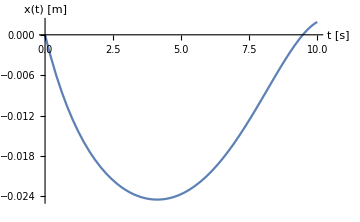
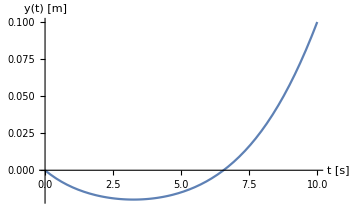
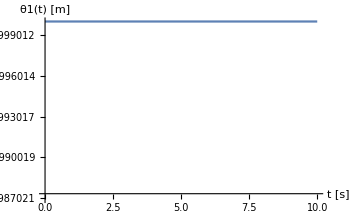
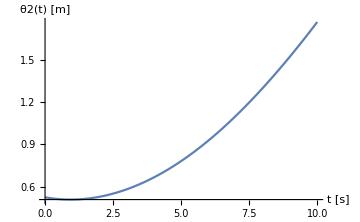
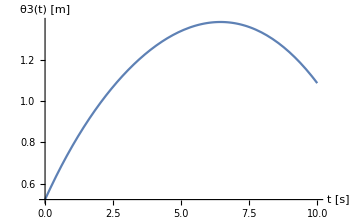

```mathematica
Row[{Plot[solMotion1[[1,2]],{t,0,10},AxesLabel->{"t [s]","x(t) [m]"},ImageSize->Medium],
Plot[solMotion1[[2,2]],{t,0,10},AxesLabel->{"t [s]","y(t) [m]"},ImageSize->Medium],
Plot[solMotion1[[3,2]],{t,0,10},AxesLabel->{"t [s]","θ1(t) [m]"},ImageSize->Medium],
Plot[solMotion1[[4,2]],{t,0,10},AxesLabel->{"t [s]","θ2(t) [m]"},ImageSize->Medium],
Plot[solMotion1[[5,2]],{t,0,10},AxesLabel->{"t [s]","θ3(t) [m]"},ImageSize->Medium]}]
```

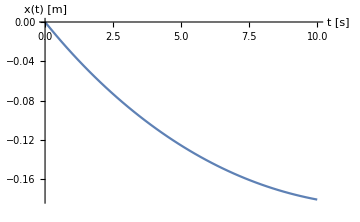
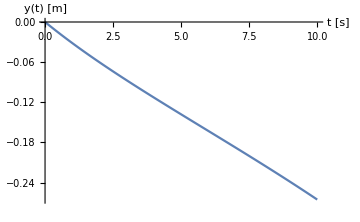
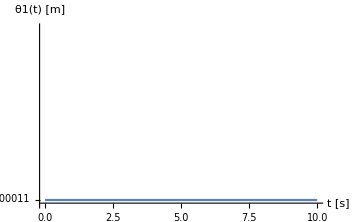
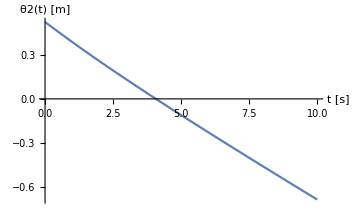
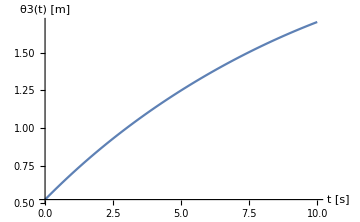

```mathematica
Row[{Plot[solMotion2[[1,2]],{t,0,10},AxesLabel->{"t [s]","x(t) [m]"},ImageSize->Medium],
Plot[solMotion2[[2,2]],{t,0,10},AxesLabel->{"t [s]","y(t) [m]"},ImageSize->Medium],
Plot[solMotion2[[3,2]],{t,0,10},AxesLabel->{"t [s]","θ1(t) [m]"},ImageSize->Medium],
Plot[solMotion2[[4,2]],{t,0,10},AxesLabel->{"t [s]","θ2(t) [m]"},ImageSize->Medium],
Plot[solMotion2[[5,2]],{t,0,10},AxesLabel->{"t [s]","θ3(t) [m]"},ImageSize->Medium]}]
```

```mathematica
paramScheme2={θ1[t]->0.2,θ2[t]->π/6,θ3[t]->π/6,x[t]->0,y[t]->0};
```

```mathematica
RobotPlot=ListLinePlot[{O1[[1;;2]]/.param/.paramScheme2,O2[[1;;2]]/.param/.paramScheme2,O3[[1;;2]]/.param/.paramScheme2},PlotRange->{{0,7},{0,7}},PlotMarkers->{Automatic, 5}];
```

```mathematica
RobotPlotAfter1=ListLinePlot[{O1[[1;;2]]/.param/.solMotion1/.t->10,O2[[1;;2]]/.param/.solMotion1/.t->10,O3[[1;;2]]/.param/.solMotion1/.t->10},PlotRange->Automatic,PlotMarkers->{Automatic, 5},PlotStyle->Dashed];
RobotPlotAfter2=ListLinePlot[{O1[[1;;2]]/.param/.solMotion2/.t->10,O2[[1;;2]]/.param/.solMotion2/.t->10,O3[[1;;2]]/.param/.solMotion2/.t->10},PlotRange->Automatic,PlotMarkers->{Automatic, 5},PlotStyle->Dashed];
```

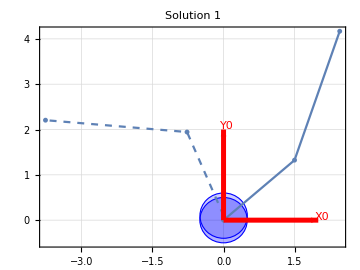
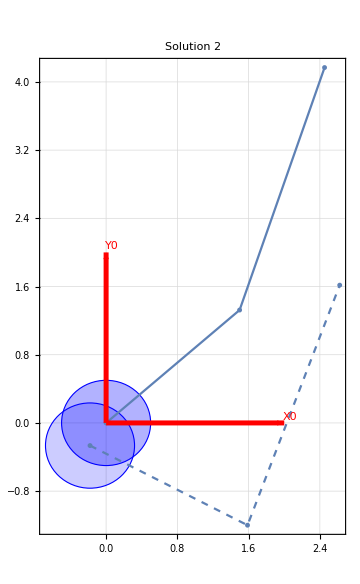

```mathematica
Row[{Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[O1[[1;;2]]/.param/.paramScheme2,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[O1[[1;;2]]/.param/.solMotion1/.t->10,r]}]],RobotPlot,RobotPlotAfter1,RF0arrow[1],RF0arrow[2]},Frame->True,GridLines->Automatic,PlotRange->Automatic,PlotLabel->"Solution 1",ImageSize->Medium],Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[O1[[1;;2]]/.param/.paramScheme2,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[O1[[1;;2]]/.param/.solMotion2/.t->10,r]}]],RobotPlot,RobotPlotAfter2,RF0arrow[1],RF0arrow[2]},Frame->True,GridLines->Automatic,PlotRange->Automatic,PlotLabel->"Solution 2",ImageSize->Medium]}]
```

### Simulation with control

Let’s suppose a critical damped behaviour (i.e. ξ=1):

```mathematica
Kp=10 IdentityMatrix[5];
Kv=2 Sqrt[Kp];
```

```mathematica
pd=p/.initialConditions1;
pd'={0,0,0,0,0};
```

```mathematica
U=Simplify[-Mp.(Kv.(pd'-p')+Kp.(pd-p))+Cp];
```

$Aborted

```mathematica
solMotionControl1=NDSolve[{(eqMotion[[1]]/.param)==U[[1]]/.param,(eqMotion[[2]]/.param)==U[[2]]/.param,(eqMotion[[3]]/.param)==U[[3]]/.param,(eqMotion[[4]]/.param)==U[[4]]/.param,(eqMotion[[5]]/.param)==U[[5]]/.param,NDinitialCondition1},{x[t],y[t],θ1[t],θ2[t],θ3[t]},{t,0,10},Method->{"EquationSimplification"->"Residual"}][[1]]
solMotionControl2=NDSolve[{(eqMotion[[1]]/.param)==U[[1]]/.param,(eqMotion[[2]]/.param)==U[[2]]/.param,(eqMotion[[3]]/.param)==U[[3]]/.param,(eqMotion[[4]]/.param)==U[[4]]/.param,(eqMotion[[5]]/.param)==U[[5]]/.param,NDinitialCondition2},{x[t],y[t],θ1[t],θ2[t],θ3[t]},{t,0,10},Method->{"EquationSimplification"->"Residual"}][[1]]
```

$Aborted